{{2,37.37,3.02044},{7,64.64,1.90512},{12,92.085,3.28705},{17,128.84,6.19616},{22,173.205,12.8858},{27,206.76,14.2799},{32,280.255,24.8626},{37,322.145,20.9782},{42,355.79,13.6789},{47,432.275,18.9087},{52,468.315,45.8623},{57,530.19,36.2364}}

{{2,38.65,2.53226},{7,180.025,24.6795},{12,919.015,126.926},{17,2480.12,291.89},{22,6461.81,1031.84},{27,16279.7,2848.11},{32,51954.1,10214.1},{37,88401.6,23024.8},{42,270473.,32280.7},{47,536595.,75634.4},{52,1.03708×10^6,225083.},{57,2.60055×10^6,478715.}}

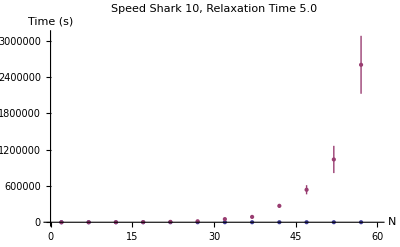

```mathematica
Needs["ErrorBarPlots`"]

dataNR={{2,37.370000,3.020440},{7,64.640000,1.905115},{12,92.085000,3.287054},{17,128.840000,6.196156},{22,173.205000,12.885783},{27,206.760000,14.279889},{32,280.255000,24.862631},{37,322.145000,20.978155},{42,355.790000,13.678906},{47,432.275000,18.908693},{52,468.315000,45.862261},{57,530.190000,36.236408}}


dataR={{2,38.650000,2.532263},{7,180.025000,24.679472},{12,919.015000,126.926088},{17,2480.120000,291.890315},{22,6461.805000,1031.844433},{27,16279.710000,2848.110963},{32,51954.100001,10214.063027},{37,88401.635000,23024.768300},{42,270473.484973,32280.653753},{47,536595.314993,75634.384950},{52,1037076.455410,225083.441305},{57,2600553.923788,478714.527087}}

ErrorListPlot[{dataNR, dataR}, AxesOrigin -> {0, 0}, PlotRange -> {{0, 60.01}, {0, 3100000}}, PlotLabel -> Style["Speed Shark 10, Relaxation Time 5.0", FontSize -> 16], AxesLabel->{Style["N",FontSize->14], Style["Time (s)",FontSize->14]}]
```